## Feature Extraction

Machine Learning algorithms center on numerical vector processing

```mathematica
NetEncoder["Characters"]["A large cat"]
```

{36,3,79,68,85,74,72,3,70,68,87}

```mathematica
NetEncoder["Tokens"]["A large cat"]
```

{11,19668,5184}

```mathematica
c = Classify[{"The cat is grey."->-Graphics-,"My cat is fast."->-Graphics-,"This dog is scary."->-Graphics-,"This is big dog"->-Graphics-},FeatureExtractor->{ToUpperCase,RemoveDiacritics,"SegmentedWords"}]
```

ClassifierFunction[…]

```mathematica
c["THIS is dog"]
```

-Graphics-

### Dimension Reduction

Encoding large amounts of complex data can be very expensive

```mathematica
NetEncoder["Image"][-Graphics-]
```

{{1},{1},{{0.184314,0.184314,0.188235,0.196078,0.207843,0.196078,0.203922,0.207843,0.203922,0.192157,0.188235,0.196078,0.207843,0.196078,0.207843,0.207843,0.2,0.196078,0.2,0.219608,0.207843,0.211765,0.203922,0.207843,0.211765,0.215686,77,0.356863,0.364706,0.356863,0.360784,0.356863,0.356863,0.372549,0.364706,0.368627,0.352941,0.360784,0.360784,0.356863,0.360784,0.376471,0.376471,0.384314,0.384314,0.388235,0.392157,0.396078,0.388235,0.4,0.392157,0.4},126,{1}}}
 |  |  |  |

```mathematica
planePoints = N[Position[ImageData@-Graphics-,0.]]
```

{{17.,25.,1.},{17.,25.,2.},{17.,25.,3.},{17.,26.,1.},{17.,26.,2.},{17.,26.,3.},{17.,27.,1.},{17.,27.,2.},{17.,27.,3.},{18.,29.,1.},{18.,29.,2.},{18.,29.,3.},{19.,28.,1.},{19.,28.,2.},{19.,28.,3.},{19.,30.,1.},1906,{52.,69.,3.},{53.,68.,1.},{53.,68.,2.},{53.,68.,3.},{53.,70.,1.},{53.,70.,2.},{53.,70.,3.},{54.,69.,1.},{54.,69.,2.},{54.,69.,3.},{55.,71.,1.},{55.,71.,2.},{55.,71.,3.},{56.,71.,1.},{56.,71.,2.},{56.,71.,3.}}
 |  |  |  |

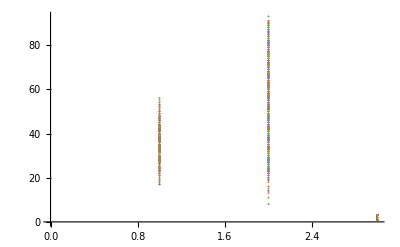

```mathematica
ListPlot[planePoints]
```

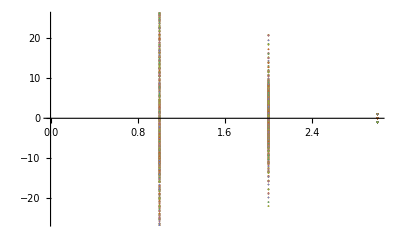

```mathematica
ListPlot[PrincipalComponents[planePoints]]
```